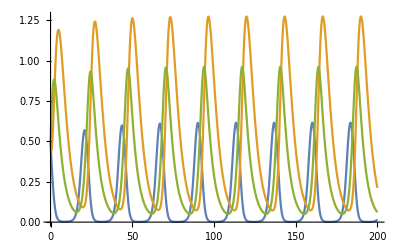

```mathematica
MetapopDyn[a_,lambda_,mu1_,mu2_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(X[t] + Y[t])*R[t] ,
X'[t] ==(1-R[t])*Y[t] - R[t]*X[t] - mu2*X[t],
Y'[t] ==-(1-R[t])*Y[t] + (lambda - mu1)*Y[t] + R[t] * X[t],
R[0]==0.5,X[0]==0.5,Y[0]==0.5},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=1,lambda=1,mu1=0.25,mu2=0.5,T=200},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,lambda,mu1,mu2,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All}]
]
```

```mathematica
Manipulate[
MetapopDyn[a_,lambda_,mu1_,mu2_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(X[t] +Y[t])*R[t] ,
X'[t] ==(1-R[t])*Y[t] - R[t]*X[t] - mu2*X[t],
Y'[t] ==-(1-R[t])*Y[t] + (lambda - mu1)*Y[t] + R[t] * X[t],
R[0]==0.5,X[0]==0.5,Y[0]==0.5},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=A,lambda=L,mu1=MU1,mu2=MU2,T=200},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,lambda,mu1,mu2,T] ];
LogPlot[Traj,{t,0,T},PlotRange->{0,All}]
],
{A,0,1},{L,0,1},{MU1,0.001,1},{MU2,0.001,1}]
```

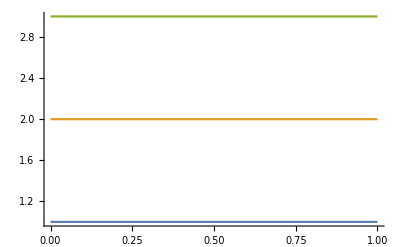

```mathematica
Plot[{x=1,x=2,x=3},{x,0,1}]
```

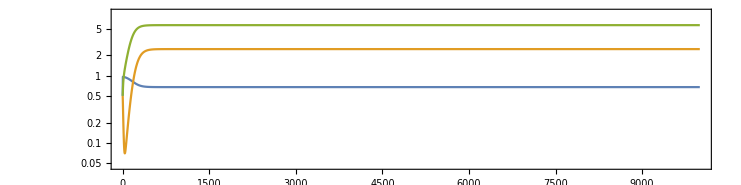

```mathematica
MetapopDyn[p_,a_,δ_,ϵ_,mux_,muy_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -ϵ*(X[t] + Y[t])*R[t] ,
X'[t] ==p*(1-R[t])*Y[t] -ϵ* R[t]*X[t] +- mux*X[t],
Y'[t] ==-p*(1-R[t])*Y[t] + δ*ϵ*Y[t]*R[t]- muy*Y[t] + ϵ*R[t] * X[t],
R[0]==0.5,X[0]==0.5,Y[0]==0.5},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{p=0.1,a=2,ϵ=0.2,δ=0.08,mux=0.02,muy=0.002,T=10000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[p,a,ϵ,δ,mux,muy,T] ];
LogPlot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True]
]
```

```mathematica
Manipulate[
MetapopDyn[a_,lambda_,muy_,p_,T_] :=

NDSolve[{
R'[t] ==a*R[t] -( Y[t])*R[t] ,
Y'[t] ==-p*(1-R[t])*Y[t] + lambda*Y[t]*R[t]- muy*Y[t] ,
R[0]==0.5,Y[0]==0.5},{R,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=1,lambda=1,muy=0.25,p=P,T=200},
Traj=Evaluate[{R[t],Y[t]}/.MetapopDyn[a,lambda,muy,p,T] ];
LogPlot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True]
],
{P,0,1}]
```

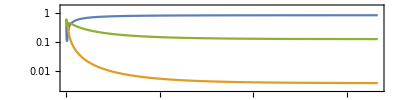

```mathematica
MetapopDyn[a_,lambda_,mux_,muy_,p_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(X[t] + Y[t])*R[t] ,
X'[t] ==p*(1-R[t])*Y[t] - R[t]*X[t] +- mux*X[t],
Y'[t] ==-p*(1-R[t])*Y[t] + lambda*Y[t]*R[t]- muy*Y[t] + R[t] * X[t],
R[0]==0.5,X[0]==0.5,Y[0]==0.5},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=1,lambda=0.003,mux=0.02,muy=0.002,p=0.2,T=5000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,lambda,mux,muy,p,T] ];
LogPlot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True]
]
```

The below code solves for the steady state

```mathematica
Sol =FullSimplify[Solve[{
0 == α*R*(1-R)-R*(X+Y),
0==σ*(1-R)*Y-ρ*R*X-μ*X,
0==γ*Y-σ*(1-R)*Y+ρ*R*X},
{R,X,Y}]]
```

{{R→0,X→0,Y→0},{R→1,X→0,Y→0},{R→(μ (-γ+σ))/(γ ρ+μ σ),X→(α γ^2 (μ+ρ))/((γ+μ) (γ ρ+μ σ)),Y→(α γ μ (μ+ρ))/((γ+μ) (γ ρ+μ σ))}}

```mathematica
InternalSol1 = Sol[[3]];
(*InternalSol2 = Sol[[4]];*)
```

```mathematica
{InternalSol1}/.{α->1,γ->0.5,μ->0.2,ρ->1,σ->0.5}
```

{{R→0.,X→0.714286,Y→0.285714}}

This means only InternalSol2 is an INTERNAL, POSITIVE SOLUTION

```mathematica
IntPosSol = InternalSol1;
```

```mathematica
Rstar = IntPosSol[[1]][[2]]
Xstar = IntPosSol[[2]][[2]]
Ystar = IntPosSol[[3]][[2]]
```

(μ (-γ+σ))/(γ ρ+μ σ)

(α γ^2 (μ+ρ))/((γ+μ) (γ ρ+μ σ))

(α γ μ (μ+ρ))/((γ+μ) (γ ρ+μ σ))

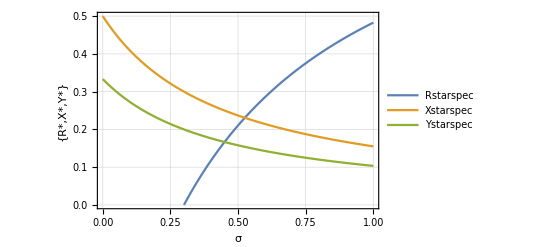

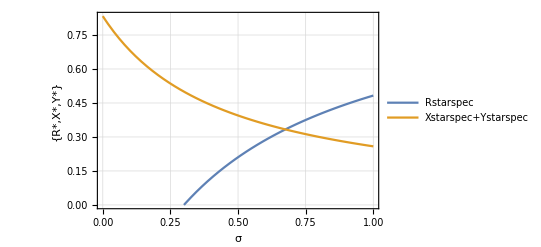

```mathematica
Rstarspec = IntPosSol[[1]][[2]]/.{α->0.5,γ->0.3,μ->0.2,ρ->0.3};
Xstarspec = IntPosSol[[2]][[2]]/.{α->0.5,γ->0.3,μ->0.2,ρ->0.3};
Ystarspec = IntPosSol[[3]][[2]]/.{α->0.5,γ->0.3,μ->0.2,ρ->0.3};
Plot[{Rstarspec,Xstarspec,Ystarspec},{σ,0,1},PlotTheme->"Detailed",FrameLabel->{"σ","{R*,X*,Y*}"},PlotRange->{0,All}]
Plot[{Rstarspec,Xstarspec+Ystarspec},{σ,0,1},PlotTheme->"Detailed",FrameLabel->{"σ","{R*,X*,Y*}"},PlotRange->{0,All}]
```

```mathematica
Limit[{Rstarspec,Xstarspec,Ystarspec},σ->Infinity]
```

{1.,0.,0.}

```mathematica
dR=   α*R*(1-R)-R*(X+Y);
dX =σ*(1-R)*Y-ρ*R*X-μ*X;
dY =γ*Y-σ*(1-R)*Y+ρ*R*X;
JacSpec = {
{D[dR,R],D[dR,X],D[dR,Y]},
{D[dX,R],D[dX,X],D[dX,Y]},
{D[dY,R],D[dY,X],D[dY,Y]}
}
```

{{-X-Y+(1-R) α-R α,-R,-R},{-X ρ-Y σ,-μ-R ρ,(1-R) σ},{X ρ+Y σ,R ρ,γ-(1-R) σ}}

```mathematica
JacSpec//MatrixForm
```

(-X-Y+(1-R) α-R α | -R | -R
-X ρ-Y σ | -μ-R ρ | (1-R) σ
X ρ+Y σ | R ρ | γ-(1-R) σ)

```mathematica
JacSpecSol =JacSpec/.{R->Rstar,X->Xstar,Y->Ystar};
```

```mathematica
(*Manipulate[
With[{
aa=A,
dd=Delta,
mmux = Mux,
pp = P
},
JacM = JacSpecSol/.{a->aa,mux->mmux,muy->mmuy,p->pp};
EV = Eigenvalues[N[JacM]];
REV = Re[EV];
MREV = Max[REV];
IEV = Im[EV];
TEV = Transpose[{REV,IEV}];
Show[{
ListPlot[TEV,PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLabel->MREV],
Graphics[Circle[]]
}]
],
{{A,2},0.0001,2},{Delta,0.0001,0.1},{{Epsilon,0.2},0.0001,2},{{Mux,0.02},0,1},{{Muy,0.002},0,1},{{P,0.1},0,1}]*)
```

Specific Bifurcations

```mathematica
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ]
```

{{σ→γ}}

```mathematica
Plot[γ/.SaddleBifAnalytic/.{σ->0.5,ρ->1,α->0.5},{μ,0,1},PlotRange->{-1,1},Frame->True]
```

-Graphics-

```mathematica
SaddleBif =Table[ {i,Min[δ/.Select[NSolve[Det[JacSpecSol/.{a->2,p->1,mux->0.02,muy->0.01,ϵ->i}] == 0,δ,Reals],(δ/.#)>0.001 &&(δ/.#)<100&]]},{i,0.1,1,0.05}];
```

```mathematica
data = SaddleBif/.{δ->0};
nlm=NonlinearModelFit[data,a*Exp[b/(c+ϵ) ],{a,b,c},ϵ]
```

FittedModel[0.00447631 ⅇ^(1.11565/(0.259928+ϵ))]

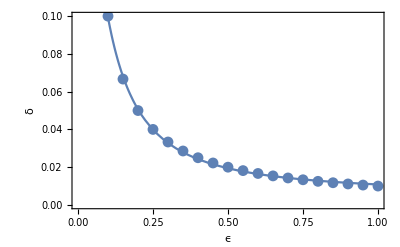

```mathematica
SNFig =Show[{
ListPlot[data,Frame->True,FrameLabel->{"ϵ","δ"}],
Plot[nlm[ϵ],{ϵ,0,1}]
}
]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/Manuscript/fig_SN.pdf",SNFig]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/Manuscript/fig_SN.pdf

```mathematica
Solve[Det[JacSpecSol/.{a->2,p->0}] == 0,δ]
```

{{δ→-muy/mux},{δ→muy/ϵ}}

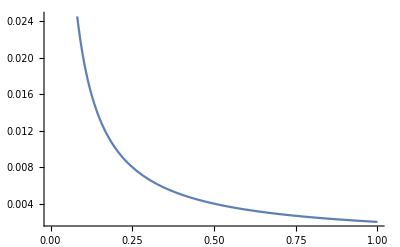

```mathematica
Plot[0.002/ϵ,{ϵ,0,1}]
```

```mathematica
deltavec = Table[x,{x,0.1,1,0.05}];
SaddleBifnum = Table[
l = Length[SaddleBif[[i]]];
x = Table[deltavec[[i]],{l}];
Transpose[{x,δ/.SaddleBif[[i]]}],
{i,1,Length[SaddleBif],1}
];
```

Transpose::nmtx: The first two levels of {{0.1, 0.1}, 0.02} cannot be transposed.

ReplaceAll::reps: {Min[δ → 0.0133333, δ → 0.0505734]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Transpose::nmtx: The first two levels of {{0.15, 0.15}, δ/. Min[δ → 0.0133333, δ → 0.0505734]} cannot be transposed.

ReplaceAll::reps: {Min[δ → 0.01, δ → 0.0749994, δ → 0.075, δ → 0.075, δ → 0.0750007, δ → 0.0750007]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Transpose::nmtx: The first two levels of {{0.2, 0.2, 0.2, 0.2, 0.2, 0.2}, δ/. Min[δ → 0.01, δ → 0.0749994, δ → 0.075, δ → 0.075, δ → 0.0750007, δ → 0.0750007]} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

ReplaceAll::reps: {Min[δ → 0.00571429, δ → 0.107144]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
ListPlot[Flatten[SaddleBifnum,1],Frame->True,FrameLabel->{"ϵ","δ"}]
```

-Graphics-

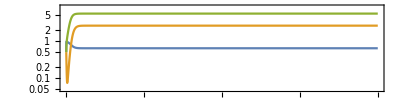

```mathematica
MetapopDyn[p_,a_,δ_,ϵ_,mux_,muy_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -ϵ*(X[t] + Y[t])*R[t] ,
X'[t] ==p*(1-R[t])*Y[t] -ϵ* R[t]*X[t] +- mux*X[t],
Y'[t] ==-p*(1-R[t])*Y[t] + δ*ϵ*Y[t]*R[t]- muy*Y[t] + ϵ*R[t] * X[t],
R[0]==0.5,X[0]==0.5,Y[0]==0.5},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{p=0.1,a=2,ϵ=0.2,δ=0.09,mux=0.02,muy=0.002,T=10000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[p,a,ϵ,δ,mux,muy,T] ];
LogPlot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True]
]
```

```mathematica
SaddleNumSol2down
```

{{0.,p},{0.1,p},{0.2,p},{0.3,p},{0.4,p},{0.5,p},{0.6,p},{0.7,p},{0.8,p},{0.9,p},{1.,p},{1.1,p},{1.2,p},{1.3,p},{1.4,p},{1.5,p},{1.6,p},{1.7,p},{1.8,p},{1.9,p},{2.,p}}

```mathematica
SaddleNumSol2up
```

{{0.,p},{0.1,p},{0.2,p},{0.3,p},{0.4,p},{0.5,p},{0.6,p},{0.7,p},{0.8,p},{0.9,p},{1.,p},{1.1,p},{1.2,p},{1.3,p},{1.4,p},{1.5,p},{1.6,p},{1.7,p},{1.8,p},{1.9,p},{2.,p}}

```mathematica
Plot3D[{muy},{mux,0,1},{muy,0,1},PlotRange->{0,All},AxesLabel->{"mux","muy","L"}]
```

-Graphics3D-

```mathematica
SylvesterMatrix=Function[{Jac},
Dim = Length[Jac];
Mat = Table[0,{Dim-1},{Dim-1}];
Col1 = Table[Subscript[ℼ,i],{i,1,(Dim-1)*2,2}];
Mat[[All,1]] = Col1;
Table[
Mat[[i]][[j]] = Subscript[ℼ,Mat[[i]][[j-1]][[2]]-1];
,{j,2,Dim-1},{i,1,Dim-1,1}];
Todel=Select[Flatten[Mat],#[[2]]<0||#[[2]]>(Dim)&];
Mat=Mat/.Table[Todel[[i]]->0,{i,1,Length[Todel],1}];
CPG = FullSimplify[CharacteristicPolynomial[Jac,λ]];
CPGL = CoefficientList[CPG,λ];
Mat2 = Mat/.Table[Subscript[ℼ,i]-> CPGL[[i+1]],{i,0,(Length[CPGL]-1),1}]
];
```

```mathematica
Sylv=SylvesterMatrix[JacSpecSol];
HopfSol=Solve[Det[Sylv]==0,muy];
```

$Aborted

```mathematica
CPG = CharacteristicPolynomial[JacSpecSol,λ];
CPGL = CoefficientList[CPG,λ];
```

```mathematica
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
```

```mathematica
HopfAnalytic = Solve[Det[Sylv]==0,γ]
```

{{γ→σ},{γ→-(α μ-μ ρ-ρ^2-2 ρ σ)/(4 ρ)-1/2 √1-1/2 √(((α μ-μ ρ-ρ^2-2 ρ σ)^2)/(2 ρ^2)-(5+ρ σ^2)/ρ-1/(3 1)-1-(1)^(1/3)/(3 2^1 ρ^2)-(-(1)^3/ρ^3+(4 (1) (-2 α μ σ-4 μ^2 σ-1+ρ σ^2))/ρ^2-(8 (7+2 μ ρ^2 σ^2))/ρ^2)/(4 √((1)^2/(4 ρ^2)-(-2 α μ σ-4 μ^2 σ-1+ρ σ^2)/ρ+1/1+(2^1 1)/(3 ρ^2 1)+(1)^(1/3)/(3 2^(1/3) ρ^2))))},{γ→1},{γ→1},{γ→-(α μ-μ ρ-ρ^2-2 ρ σ)/(4 ρ)+1/2 √(((α μ-μ ρ-ρ^2-2 ρ σ)^2)/(4 ρ^2)-(-2 α μ σ-4 μ^2 σ-4 μ ρ σ+ρ σ^2)/ρ+(-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)/(3 ρ^2)+(2^(1/3) ((-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^2-3 (α μ ρ-μ ρ^2-ρ^3-2 ρ^2 σ) (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2)+12 ρ^2 (α μ^3 σ^2+μ^4 σ^2+α μ^2 ρ σ^2+2 μ^3 ρ σ^2+μ^2 ρ^2 σ^2)))/(3 ρ^2 (2 (-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^3-9 (α μ ρ-μ ρ^2-ρ^3-2 ρ^2 σ) (1) (1)+4+√(-4 ((1)^2-1+1)^3+(1)^2))^(1/3))+((7+√(-4 ((1)^2-3 1 (1)+12 ρ^2 (α μ^3 σ^2+4))^3+(1)^2))^(1/3))/(3 2^(1/3) ρ^2))+1/2 √(((α μ-μ ρ-ρ^2-2 ρ σ)^2)/(2 ρ^2)-(-2 α μ σ-4 μ^2 σ-4 μ ρ σ+ρ σ^2)/ρ-(-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)/(3 ρ^2)-(2^(1/3) ((-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^2-3 (α μ ρ-μ ρ^2-ρ^3-2 ρ^2 σ) (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2)+12 ρ^2 (α μ^3 σ^2+μ^4 σ^2+α μ^2 ρ σ^2+2 μ^3 ρ σ^2+μ^2 ρ^2 σ^2)))/(3 ρ^2 (2 (-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^3-9 (α μ ρ-μ ρ^2-ρ^3-2 ρ^2 σ) (1) (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2)+4+√(-4 ((-2 α μ ρ σ-4 μ^2 ρ σ-4 μ 1 σ+ρ^2 σ^2)^2-3 (1) (1)+12 ρ^2 (α μ^3 σ^2+μ^4 σ^2+α μ^2 ρ σ^2+2 μ^3 ρ σ^2+μ^2 ρ^2 σ^2))^3+(1)^2))^(1/3))-1/(3 2^(1/3) ρ^2)(2 (-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^3-9 (α μ ρ-μ ρ^2-ρ^3-2 ρ^2 σ) (-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2) (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2)+4+√(-4 ((-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^2-3 (1) (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2)+12 ρ^2 (α μ^3 σ^2+μ^4 σ^2+α μ^2 ρ σ^2+2 μ^3 ρ σ^2+μ^2 ρ^2 σ^2))^3+(1)^2))^(1/3)+(-((α μ-μ ρ-ρ^2-2 ρ σ)^3)/ρ^3+(4 (α μ-μ ρ-ρ^2-2 ρ σ) (-2 α μ σ-4 μ^2 σ-4 μ ρ σ+ρ σ^2))/ρ^2-(8 (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2))/ρ^2)/(4 √(((α μ-μ ρ-ρ^2-2 ρ σ)^2)/(4 ρ^2)-(-2 α μ σ-4 μ^2 σ-4 μ ρ σ+ρ σ^2)/ρ+(-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)/(3 ρ^2)+(2^(1/3) ((-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^2-3 (α μ ρ-μ ρ^2-ρ^3-2 ρ^2 σ) (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2)+12 ρ^2 (α μ^3 σ^2+μ^4 σ^2+α μ^2 ρ σ^2+2 μ^3 ρ σ^2+μ^2 ρ^2 σ^2)))/(3 ρ^2 (2 (-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^3-9 (α μ ρ-μ ρ^2-ρ^3-2 ρ^2 σ) (1) (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2)+1+1-1+√(-4 ((5+1)^2-1+12 ρ^2 (α μ^3 σ^2+3+μ^2 ρ^2 σ^2))^3+(1)^2))^(1/3))+((7+√(-4 ((-2 α μ ρ σ-4 2 σ-1+ρ^2 σ^2)^2-3 (1) (1)+12 ρ^2 (α μ^3 σ^2+3+μ^2 ρ^2 σ^2))^3+(1)^2))^(1/3))/(3 2^(1/3) ρ^2))))}}
 |  |  |  |

The solution to the Hopf Bifurcation surface may not be analytically tractable
Try Solving numerically with a = 1

```mathematica
HopfNumSol2down=ParallelTable[{i,Quiet[Min[σ/.Select[NSolve[Det[Sylv/.{α->1,μ->0.02,ρ->i,γ->i}]==0,σ,Reals],(σ/.#)>0.001 &&(σ/.#)<100& ]]]},{i,0,1,0.001}];
HopfNumSol2up=ParallelTable[{i,Quiet[Max[σ/.Select[NSolve[Det[Sylv/.{α->1,μ->0.02,ρ->i,γ->i}]==0,σ,Reals],(σ/.#)>0.001&&(σ/.#)<100& ]]]},{i,0,1,0.001}];
```

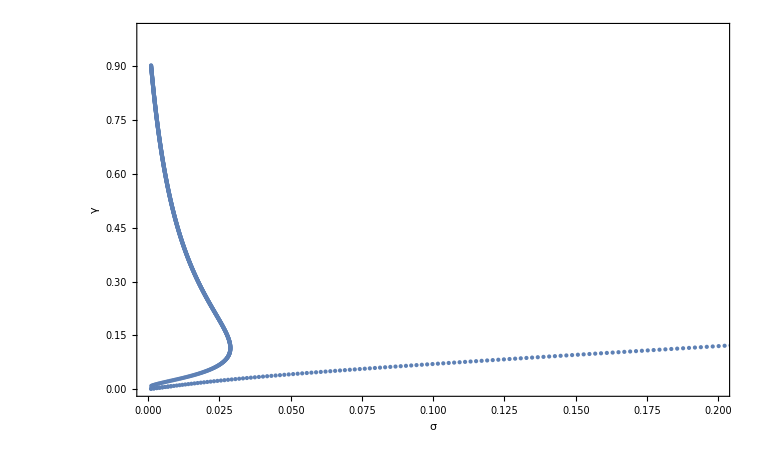

```mathematica
ListPlot[{Reverse[HopfNumSol2down,2]/.σ->Infinity,Reverse[HopfNumSol2up,2]/.σ->Infinity},Frame->True,Joined->False,FrameLabel->{"σ","γ"},PlotRange->{{0,0.2},{0,1}},PlotStyle->Directive[{ColorData[97,1],PointSize->Small}]]
```

```mathematica
HopfData=Join[{Reverse[HopfNumSol2down,2]/.σ->"NA",Reverse[HopfNumSol2up,2]/.σ->"NA"}];
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/HopfData.csv",Flatten[HopfData,1],"CSV"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/HopfData.csv

```mathematica
X=Select[Solve[Det[Sylv/.{a->1,mux->0.25,muy->0.5,L->9}]==0,p,Reals],(p/.#)>0.001&]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p→0.093492},{p→3.25827}}

```mathematica
p/.X
```

{0.093492,3.25827}

```mathematica
HopfNumSol2/.p->0
```

{{0.,0},{0.1,{1.32588}},{0.2,{3.56318}},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1.,0},{1.1,0},{1.2,0},{1.3,0},{1.4,0},{1.5,0},{1.6,0},{1.7,0},{1.8,0},{1.9,0},{2.,0},{2.1,0},{2.2,0},{2.3,0},{2.4,0},{2.5,0},{2.6,0},{2.7,0},{2.8,0},{2.9,0},{3.,0},{3.1,0},{3.2,0},{3.3,0},{3.4,0},{3.5,0},{3.6,0},{3.7,0},{3.8,0},{3.9,0},{4.,0},{4.1,0},{4.2,0},{4.3,0},{4.4,{0.480607,0.884594}},{4.5,{0.420835,0.999427}},{4.6,{0.380429,1.09404}},{4.7,{0.349654,1.1782}},{4.8,{0.324823,1.25564}},{4.9,{0.304079,1.32824}},{5.,{0.286333,1.39713}},{5.1,{0.270888,1.46303}},{5.2,{0.257265,1.52645}},{5.3,{0.245121,1.58775}},{5.4,{0.234202,1.64722}},{5.5,{0.224313,1.70508}},{5.6,{0.2153,1.76149}},{5.7,{0.207044,1.8166}},{5.8,{0.199444,1.87053}},{5.9,{0.192419,1.92337}},{6.,{0.185903,1.97522}},{6.1,{0.179839,2.02614}},{6.2,{0.174178,2.0762}},{6.3,{0.168878,2.12546}},{6.4,{0.163906,2.17395}},{6.5,{0.15923,2.22173}},{6.6,{0.154822,2.26884}},{6.7,{0.15066,2.31532}},{6.8,{0.146723,2.36118}},{6.9,{0.142992,2.40647}},{7.,{0.139451,2.45121}},{7.1,{0.136085,2.49542}},{7.2,{0.132882,2.53914}},{7.3,{0.129829,2.58237}},{7.4,{0.126915,2.62513}},{7.5,{0.124132,2.66746}},{7.6,{0.12147,2.70935}},{7.7,{0.118922,2.75084}},{7.8,{0.116479,2.79192}},{7.9,{0.114137,2.83263}},{8.,{0.111887,2.87296}},{8.1,{0.109725,2.91293}},{8.2,{0.107647,2.95256}},{8.3,{0.105646,2.99185}},{8.4,{0.103718,3.03082}},{8.5,{0.10186,3.06947}},{8.6,{0.100068,3.10781}},{8.7,{0.0983386,3.14585}},{8.8,{0.0966679,3.1836}},{8.9,{0.0950533,3.22107}},{9.,{0.093492,3.25827}},{9.1,{0.0919812,3.2952}},{9.2,{0.0905187,3.33187}},{9.3,{0.089102,3.36828}},{9.4,{0.0877291,3.40445}},{9.5,{0.0863979,3.44037}},{9.6,{0.0851065,3.47606}},{9.7,{0.0838532,3.51152}},{9.8,{0.0826363,3.54675}},{9.9,{0.0814542,3.58177}},{10.,{0.0803054,3.61656}}}

```mathematica
Length[Table[i,{i,0,1,0.01}]]
Length[Table[i,{i,1,7,0.05}]]
```

101

121

```mathematica
HopfNumSol2=ParallelTable[{i,j,Select[Solve[Det[Sylv/.{a->1,mux->0.5,muy->i,L->j}]==0,p,Reals],(p/.#)>0.001&][[1]][[1]][[2]]},{i,0,1,0.01},{j,1,7,0.05}];
```

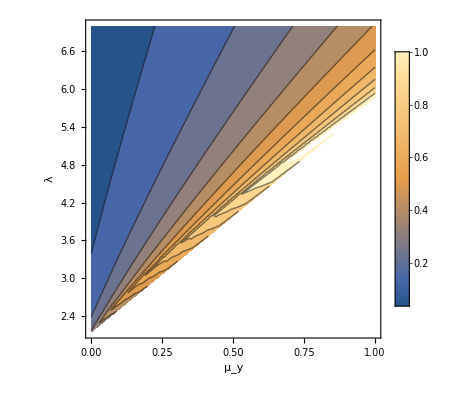

```mathematica
Show[{
ListContourPlot[Flatten[HopfNumSol2,1],PlotRange->{0,1},PlotLegends->{Table[i,{i,0,1,0.01}]},
FrameLabel->{"μ_y","λ"},Contours->10(*,RegionFunction->Function[{x,y,z},y>x]*)],
Graphics[{PointSize[Medium],White,Point[{0.25,0.5}]}]
}]
```

```mathematica
HopfNumSol=ParallelTable[{i,j,Quiet[Select[Solve[Det[Sylv/.{a->1,k->2,mux->j,muy->i,L->1}]==0,p,Reals],(p/.#)>0.001&][[1]][[1]][[2]]]},{i,0,1,0.01},{j,0,1,0.01}];
```

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

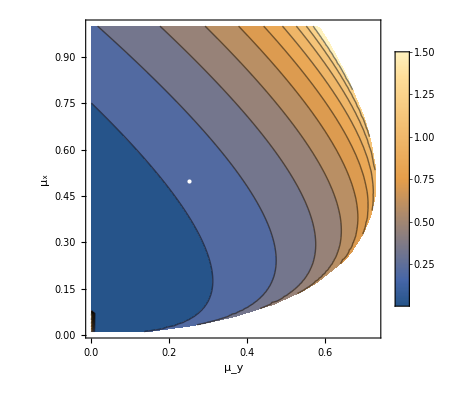

```mathematica
Show[{
ListContourPlot[Flatten[HopfNumSol,1],PlotRange->{0,1.5},PlotLegends->{Table[i,{i,0,1,0.01}]},
FrameLabel->{"μ_y","μ_x"},Contours->10(*,RegionFunction->Function[{x,y,z},y>x]*)],
Graphics[{PointSize[Medium],White,Point[{0.25,0.5}]}]
}]
```

Generalized model

```mathematica
JacMGen = 
{
{ar*(dsdr - dldr),-ar*dldx,-ar*dldy},
{ax*(dfdr - bx*dgdr),-ax*(bx*dgdx + (1-bx)*dmdx),ax*dfdy},
{ay*(dy*dhdr+(1-dy)*dgdr-by*dfdr),ay*(1-dy)*dgdx,ay*(dy*dhdy-by*dfdy-(1-by)*dmdy)}
};
```

```mathematica
JacMGen// MatrixForm
```

(ar (-dldr+dsdr) | -ar dldx | -ar dldy
ax (dfdr-bx dgdr) | -ax (bx dgdx+(1-bx) dmdx) | ax dfdy
ay (-by dfdr+dgdr (1-dy)+dhdr dy) | ay dgdx (1-dy) | ay (-by dfdy-(1-by) dmdy+dhdy dy))

```mathematica
Manipulate[
With[{
ar = 0.5,
ax = 1,
ay = 0.5,
bx = BX,
dy = DY,
by = BY,
dsdr = DSDR,
dldr  = 1,
dldx=DLDX,
dldy = 1-DLDX,
dfdr = DFDR,
dfdy = 1,
dgdr = 1,
dgdx = 1,
dhdr = 1,
dhdy = 1,
dmdx = 1,
dmdy = 1
},
JacM = 
{
{ar*(dsdr - dldr),-ar*dldx,-ar*dldy},
{ax*(dfdr - bx*dgdr),-ax*(bx*dgdx + (1-bx)*dmdx),ax*dfdy},
{ay*(dy*dhdr+(1-dy)*dgdr-by*dfdr),ay*(1-dy)*dgdx,ay*(dy*dhdy-by*dfdy-(1-by)*dmdy)}
};
EV = Eigenvalues[N[JacM]];
REV = Re[EV];
IEV = Im[EV];
TEV = Transpose[{REV,IEV}];
ListPlot[TEV,PlotRange->{{-2,2},{-2,2}}]
]
,{BX,0,1},{DY,0,1},{BY,0,1},{DSDR,-1,0},{DLDX,0,1},{DFDR,-1,0}]
```

```mathematica
JacGen = 
{
{ar*(dsdr - dldr),-ar*dldx,-ar*dldy},
{ax*(dfdr - bx*dgdr),-ax*(bx*dgdx + (1-bx)*dmdx),ax*dfdy},
{ay*((1-dy)*dgdr-by*dfdr),ay*(1-dy)*dgdx,ay*(dy*dhdy-by*dfdy-(1-by)*dmdy)}
};
```

```mathematica
Saddlegen =FullSimplify[ Solve[Det[JacGen]==0,dsdr]]
```

{{dsdr→(-dgdr dldy dmdx+bx dgdr dldy dmdx-bx dgdx dldr dmdy+bx by dgdx dldr dmdy+bx dgdr dldx dmdy-bx by dgdr dldx dmdy-dldr dmdx dmdy+bx dldr dmdx dmdy+by dldr dmdx dmdy-bx by dldr dmdx dmdy+(bx dhdy (dgdx dldr-dgdr dldx)-(-1+bx) (dhdy dldr+dgdr dldy) dmdx) dy+dfdy ((-1+bx) by dldr dmdx-dgdx dldr (-1+bx by+dy)+dgdr dldx (-1+bx by+dy))+dfdr (-dldx dmdy+by (dldy dmdx-bx dldy dmdx+dldx dmdy)+dhdy dldx dy+dgdx dldy (-1+bx by+dy)))/((bx (dgdx-dmdx)+dmdx) ((-1+by) dmdy+dhdy dy)+dfdy ((-1+bx) by dmdx-dgdx (-1+bx by+dy)))}}

```mathematica
CPGgen = FullSimplify[CharacteristicPolynomial[JacGen,λ]];
CPGLgen = CoefficientList[CPGgen,λ];
Sylvgen = {{CPGLgen[[2]],CPGLgen[[1]]},{CPGLgen[[4]],CPGLgen[[3]]}} ;
```

```mathematica
Sylvgen//MatrixForm
```

(-ar ax (dfdr-bx dgdr) dldx-ar ax (bx (dgdx-dmdx)+dmdx) (dldr-dsdr)+ar ay dldy (by dfdr+dgdr (-1+dy))-ax ay dfdy dgdx (-1+dy)+ax ay (bx (dgdx-dmdx)+dmdx) (-dmdy+by (-dfdy+dmdy)+dhdy dy)+ar ay (dldr-dsdr) (-dmdy+by (-dfdy+dmdy)+dhdy dy) | ar ax ay (dfdy dldx+dldy (bx dgdx+dmdx-bx dmdx)) (by dfdr+dgdr (-1+dy))-ar ax ay dgdx (-dfdr dldy+bx dgdr dldy+dfdy (dldr-dsdr)) (-1+dy)+ar ax ay (dfdr-bx dgdr) dldx (-dmdy+by (-dfdy+dmdy)+dhdy dy)+ar ax ay (bx (dgdx-dmdx)+dmdx) (dldr-dsdr) (-dmdy+by (-dfdy+dmdy)+dhdy dy)
-1 | -ax (bx (dgdx-dmdx)+dmdx)-ar (dldr-dsdr)+ay (-dmdy+by (-dfdy+dmdy)+dhdy dy))

```mathematica
HopfGen=Simplify[Solve[Det[Sylvgen]==0,dsdr]]
```

{{dsdr→(ar ay^2 by^2 dfdy^2+2 ar ax ay bx by dfdy dgdx+ar ax^2 bx^2 dgdx^2+2 ar^2 ay by dfdy dldr+2 ar^2 ax bx dgdx dldr+ar^2 ax dfdr dldx-ar^2 ax bx dgdr dldx-ar^2 ay by dfdr dldy+ar^2 ay dgdr dldy+2 ar ax ay by dfdy dmdx-2 ar ax ay bx by dfdy dmdx+2 ar ax^2 bx dgdx dmdx-2 ar ax^2 bx^2 dgdx dmdx+2 ar^2 ax dldr dmdx-2 ar^2 ax bx dldr dmdx+ar ax^2 dmdx^2-2 ar ax^2 bx dmdx^2+ar ax^2 bx^2 dmdx^2+2 ar ay^2 by dfdy dmdy-2 ar ay^2 by^2 dfdy dmdy+2 ar ax ay bx dgdx dmdy-2 ar ax ay bx by dgdx dmdy+2 ar^2 ay dldr dmdy-2 ar^2 ay by dldr dmdy+2 ar ax ay dmdx dmdy-2 ar ax ay bx dmdx dmdy-2 ar ax ay by dmdx dmdy+2 ar ax ay bx by dmdx dmdy+ar ay^2 dmdy^2-2 ar ay^2 by dmdy^2+ar ay^2 by^2 dmdy^2-2 ar ay^2 by dfdy dhdy dy-2 ar ax ay bx dgdx dhdy dy-2 ar^2 ay dhdy dldr dy-ar^2 ay dgdr dldy dy-2 ar ax ay dhdy dmdx dy+2 ar ax ay bx dhdy dmdx dy-2 ar ay^2 dhdy dmdy dy+2 ar ay^2 by dhdy dmdy dy+ar ay^2 dhdy^2 dy^2-√(ar^2 ((ax (ax (bx (dgdx-dmdx)+dmdx)^2+ar (dfdr dldx+2 dldr dmdx+bx (2 dgdx dldr-dgdr dldx-2 dldr dmdx)))+ay^2 (by (dfdy-dmdy)+dmdy-dhdy dy)^2+ay (2 ax (bx (dgdx-dmdx)+dmdx) (by (dfdy-dmdy)+dmdy-dhdy dy)-ar (by (-2 dfdy dldr+dfdr dldy+2 dldr dmdy)+dgdr dldy (-1+dy)-2 dldr (dmdy-dhdy dy))))^2-4 (ax (bx (dgdx-dmdx)+dmdx)+ay (by (dfdy-dmdy)+dmdy-dhdy dy)) (ar ay (ar dldr+ay (by (dfdy-dmdy)+dmdy-dhdy dy)) (by (dfdy dldr-dfdr dldy-dldr dmdy)+dldr (dmdy-dhdy dy)+dgdr (dldy-dldy dy))+ax^2 (bx (dgdx-dmdx)+dmdx) (ar (dfdr dldx+dldr dmdx+bx (dgdx dldr-dgdr dldx-dldr dmdx))+ay (-(bx (dgdx-dmdx)+dmdx) ((-1+by) dmdy+dhdy dy)+dfdy (-(-1+bx) by dmdx+dgdx (-1+bx by+dy))))+ax (ar^2 dldr (dfdr dldx+dldr dmdx+bx (dgdx dldr-dgdr dldx-dldr dmdx))+ay^2 (by (dfdy-dmdy)+dmdy-dhdy dy) (-(bx (dgdx-dmdx)+dmdx) ((-1+by) dmdy+dhdy dy)+dfdy (-(-1+bx) by dmdx+dgdx (-1+bx by+dy)))+ar ay (by dfdr dfdy dldx-dfdy dgdr dldx-dfdr dgdx dldy+2 by dfdy dldr dmdx+2 dldr dmdx dmdy-2 by dldr dmdx dmdy+dfdy dgdr dldx dy+dfdr dgdx dldy dy-2 dhdy dldr dmdx dy+bx (2 by dldr (dgdx-dmdx) (dfdy-dmdy)-dgdr dgdx dldy (-1+dy)+2 dldr (dgdx-dmdx) (dmdy-dhdy dy))))))))/(2 ar^2 (ax (bx (dgdx-dmdx)+dmdx)+ay (by (dfdy-dmdy)+dmdy-dhdy dy)))},{dsdr→(ar ay^2 by^2 dfdy^2+2 ar ax ay bx by dfdy dgdx+ar ax^2 bx^2 dgdx^2+2 ar^2 ay by dfdy dldr+2 ar^2 ax bx dgdx dldr+ar^2 ax dfdr dldx-ar^2 ax bx dgdr dldx-ar^2 ay by dfdr dldy+ar^2 ay dgdr dldy+2 ar ax ay by dfdy dmdx-2 ar ax ay bx by dfdy dmdx+2 ar ax^2 bx dgdx dmdx-2 ar ax^2 bx^2 dgdx dmdx+2 ar^2 ax dldr dmdx-2 ar^2 ax bx dldr dmdx+ar ax^2 dmdx^2-2 ar ax^2 bx dmdx^2+ar ax^2 bx^2 dmdx^2+2 ar ay^2 by dfdy dmdy-2 ar ay^2 by^2 dfdy dmdy+2 ar ax ay bx dgdx dmdy-2 ar ax ay bx by dgdx dmdy+2 ar^2 ay dldr dmdy-2 ar^2 ay by dldr dmdy+2 ar ax ay dmdx dmdy-2 ar ax ay bx dmdx dmdy-2 ar ax ay by dmdx dmdy+2 ar ax ay bx by dmdx dmdy+ar ay^2 dmdy^2-2 ar ay^2 by dmdy^2+ar ay^2 by^2 dmdy^2-2 ar ay^2 by dfdy dhdy dy-2 ar ax ay bx dgdx dhdy dy-2 ar^2 ay dhdy dldr dy-ar^2 ay dgdr dldy dy-2 ar ax ay dhdy dmdx dy+2 ar ax ay bx dhdy dmdx dy-2 ar ay^2 dhdy dmdy dy+2 ar ay^2 by dhdy dmdy dy+ar ay^2 dhdy^2 dy^2+√(ar^2 ((ax (ax (bx (dgdx-dmdx)+dmdx)^2+ar (dfdr dldx+2 dldr dmdx+bx (2 dgdx dldr-dgdr dldx-2 dldr dmdx)))+ay^2 (by (dfdy-dmdy)+dmdy-dhdy dy)^2+ay (2 ax (bx (dgdx-dmdx)+dmdx) (by (dfdy-dmdy)+dmdy-dhdy dy)-ar (by (-2 dfdy dldr+dfdr dldy+2 dldr dmdy)+dgdr dldy (-1+dy)-2 dldr (dmdy-dhdy dy))))^2-4 (ax (bx (dgdx-dmdx)+dmdx)+ay (by (dfdy-dmdy)+dmdy-dhdy dy)) (ar ay (ar dldr+ay (by (dfdy-dmdy)+dmdy-dhdy dy)) (by (dfdy dldr-dfdr dldy-dldr dmdy)+dldr (dmdy-dhdy dy)+dgdr (dldy-dldy dy))+ax^2 (bx (dgdx-dmdx)+dmdx) (ar (dfdr dldx+dldr dmdx+bx (dgdx dldr-dgdr dldx-dldr dmdx))+ay (-(bx (dgdx-dmdx)+dmdx) ((-1+by) dmdy+dhdy dy)+dfdy (-(-1+bx) by dmdx+dgdx (-1+bx by+dy))))+ax (ar^2 dldr (dfdr dldx+dldr dmdx+bx (dgdx dldr-dgdr dldx-dldr dmdx))+ay^2 (by (dfdy-dmdy)+dmdy-dhdy dy) (-(bx (dgdx-dmdx)+dmdx) ((-1+by) dmdy+dhdy dy)+dfdy (-(-1+bx) by dmdx+dgdx (-1+bx by+dy)))+ar ay (by dfdr dfdy dldx-dfdy dgdr dldx-dfdr dgdx dldy+2 by dfdy dldr dmdx+2 dldr dmdx dmdy-2 by dldr dmdx dmdy+dfdy dgdr dldx dy+dfdr dgdx dldy dy-2 dhdy dldr dmdx dy+bx (2 by dldr (dgdx-dmdx) (dfdy-dmdy)-dgdr dgdx dldy (-1+dy)+2 dldr (dgdx-dmdx) (dmdy-dhdy dy))))))))/(2 ar^2 (ax (bx (dgdx-dmdx)+dmdx)+ay (by (dfdy-dmdy)+dmdy-dhdy dy)))}}

```mathematica
Saddlegen1 = Saddlegen[[1]][[1]][[2]]/.{
ar -> 1,
ax -> 1,
ay -> 1,
bx -> BX,
dy -> DY,
by -> BY,
(*dsdr -> -0.5,*)
dldr  -> 1,
dldx->DLDX,
dldy -> 1-DLDX,
dfdr -> DFDR,
dfdy -> 1,
dgdr -> 1,
dgdx -> 1,
dhdr -> 1,
dhdy -> 1,
dmdx -> 1,
dmdy -> 1}
HopfGen1 = HopfGen[[1]][[1]][[2]]/.{
ar -> 1,
ax -> 1,
ay -> 1,
bx -> BX,
dy -> DY,
by -> BY,
(*dsdr -> -0.5,*)
dldr  -> 1,
dldx->DLDX,
dldy -> 1-DLDX,
dfdr -> DFDR,
dfdy -> 1,
dgdr -> 1,
dgdx -> 1,
dhdr -> 1,
dhdy -> 1,
dmdx -> 1,
dmdy -> 1}
```

1/(BY+(-1+BX) BY-BX BY)(-1+BY+(-1+BX) BY-BX BY+BX (1-DLDX)+DLDX+BX DLDX-BX BY DLDX-DY+(BX (1-DLDX)-(-1+BX) (2-DLDX)) DY+DLDX (-1+BX BY+DY)+DFDR (BY (1-BX (1-DLDX))-DLDX+DLDX DY+(1-DLDX) (-1+BX BY+DY)))

1/(2 (2-DY))(9-BY DFDR (1-DLDX)-DLDX-BX DLDX+DFDR DLDX-6 DY-(1-DLDX) DY+DY^2-√((3-BY DFDR (1-DLDX)-BX DLDX+DFDR DLDX+4 (1-DY)+(1-DY)^2-(1-DLDX) (-1+DY))^2-4 (2-DY) (4-BY-(-1+BX) BY+BX BY-DFDR (1-DLDX)-DLDX-2 BX DLDX+2 DFDR DLDX+BY DFDR DLDX+(-BY-(-1+BX) BY+BX BY) (1-DY)-BX (1-DLDX) (-1+DY)-2 DY+DFDR (1-DLDX) DY+DLDX DY+(2-DY) (2-BY DFDR (1-DLDX)-DLDX-DY-(1-DLDX) DY))))

```mathematica
Plot3D[HopfGen1/.{
BX->0.8,
DY->0.8,
BY->0.8
},{DLDX,0,1},{DFDR,-1,0},PlotRange->{-1,1},ClippingStyle->None]
```

-Graphics3D-

```mathematica
Solve[{ay+L*ar==L,r==ay/ar},r]
```

{}

```mathematica
JacGenSpec = {
{ar*(dsdr - dldr),-ar*dldx,-ar*dldy},
{ax*(dfdr - bx*dgdr),-ax*(bx*dgdx + (1-bx)*dmdx),ax*dfdy},
{ay*(dy*dhdr+(1-dy)*dgdr-by*dfdr),ay*(1-dy)*dgdx,ay*(dy*dhdy-by*dfdy-(1-by)*dmdy)}
}/.{
dldr -> 1,
dfdy -> 1,
dgdr -> 1,
dgdx -> 1,
dhdr -> 1,
dhdy -> 1,
dmdx -> 1,
dmdy -> 1,
dldy->1-dldx
};
```

```mathematica
JacGenSpec //MatrixForm
```

(ar (-1+dsdr) | -ar dldx | -ar (1-dldx)
ax (-bx+dfdr) | -ax | ax
ay (1-by dfdr) | ay (1-dy) | ay (-1+dy))

```mathematica
CPGgen = FullSimplify[CharacteristicPolynomial[JacGenSpec,λ]];
CPGLgen = CoefficientList[CPGgen,λ];
Sylvgen = {{CPGLgen[[2]],CPGLgen[[1]]},{CPGLgen[[4]],CPGLgen[[3]]}} ;
```

```mathematica
Sylvgen//MatrixForm
```

(ar ax (-1+bx dldx-dfdr dldx+dsdr)+ar ay (-2+by dfdr+dldx-by dfdr dldx+dsdr+dy-dsdr dy) | ar ax ay (-1+bx-bx dy+dfdr (-1+by+dy))
-1 | -ax-ay+ar (-1+dsdr)+ay dy)

```mathematica
HopfGen=Simplify[Solve[Det[Sylvgen]==0,ar]]
```

{{ar→0},{ar→(ax^2 (-1+bx dldx-dfdr dldx+dsdr)+ay^2 (-1+dy) (2+by dfdr (-1+dldx)-dldx-dsdr-dy+dsdr dy)+ax ay (-2+dldx+2 dsdr+2 dy-2 dsdr dy+bx (-1+dldx+dy-dldx dy)-dfdr (-1+dldx+by dldx+dy-dldx dy)))/((-1+dsdr) (ax (-1+bx dldx-dfdr dldx+dsdr)+ay (-2+dldx+by (dfdr-dfdr dldx)+dsdr+dy-dsdr dy)))}}

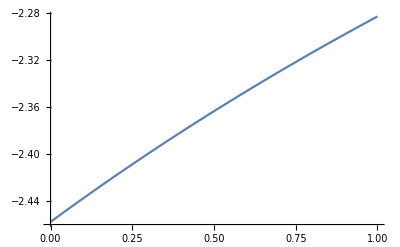

```mathematica
Plot[HopfGen[[1]][[1]][[2]]/.{ar->1,ax->0.5,dsdr->-0.5,dldx->0.5,dfdr->-0.5,bx->0.25,dy->0.25},{by,0,1}]
```

```mathematica
Manipulate[
Plot3D[{HopfGen[[2]][[1]][[2]]}/.{ax->AX,dsdr->DSDR,dldx->DLDX,dfdr->DFDR,bx->BX,dy->DY},{ay,0,2},{by,0,1},PlotRange->{0,2},AxesLabel->{"ay","by","ar"}],
{AX,0,1},
{DSDR,-1,0},
{DLDX,0,1},
{DFDR,-1,0},
{BX,0,1},
{DY,0,1}
]
```